```mathematica
qubits=Import["~/projects/QUORA/qubits.csv"]
```

{{1998,2},{1998,2},{2000,5},{2000,7},{2006,12},{2017,17},{2017,50},{2018,72}}

```mathematica
f=Fit[qubits, {1,x,ⅇ^x},x]
```

-1088.17+2.2007718043585×10^-875 ⅇ^x+0.546595 x

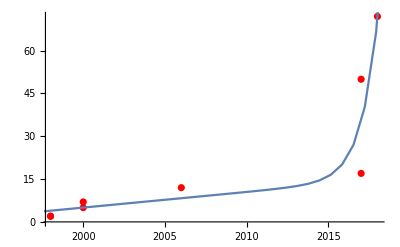

```mathematica
Show[ListPlot[qubits, PlotStyle->  Red], Plot[f, {x, 0, 2020}], Evaluated-> True]
```

```mathematica
f/.x-> 2019
```

167.854

```mathematica
Table[{y,f/.x-> y}, {y, 2018, 2025}]
```

{{2018,70.9397},{2019,167.854},{2020,430.357},{2021,1142.97},{2022,3079.13},{2023,8341.2},{2024,22644.1},{2025,61522.3}}